# Cleaning Data

```mathematica
SetDirectory[NotebookDirectory[]];
rawData=Import["connect.csv"];
headlessData=rawData[[2;;All]][[All,2;;All]];
Export["cleanData.csv",headlessData]
```

# Find Communities

```mathematica
graph=WeightedAdjacencyGraph[headlessData];
communities=FindGraphCommunities[graph];
Export["communities.csv",communities]
```

communities.csv

# Draw Map

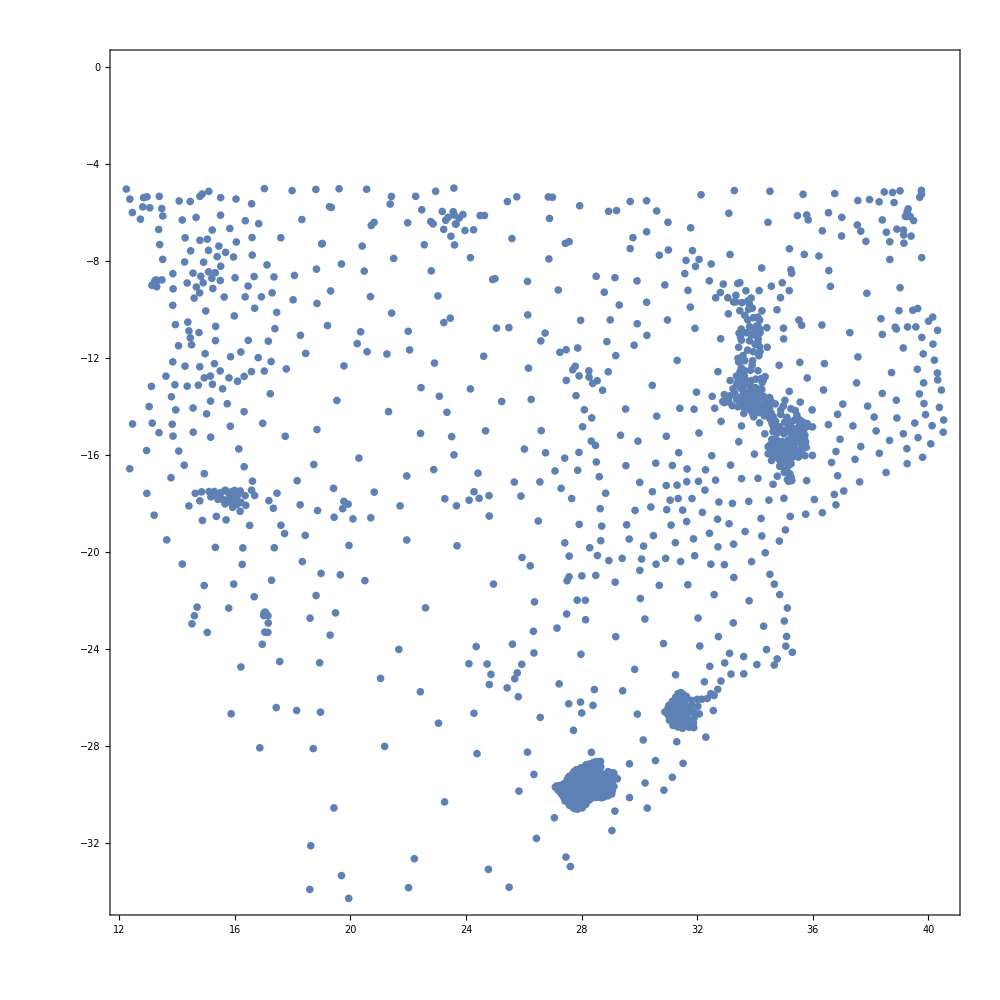

```mathematica
longlats=Import["longlat.csv"][[2;;All]][[All,2;;All]];
ListPlot[longlats
,AspectRatio->1
,Frame->True
,FrameStyle->Thick
,ImageSize->1000
]
```

```mathematica
communities//Length
```

217

```mathematica
colors=ColorData[{"TemperatureMap","Reverse"}][#/(communities//Length)]&/@(Range[1,communities//Length]);
colors//Length
```

217

```mathematica
ListPlot[longlats
,AspectRatio->1
,Frame->True
,FrameStyle->Thick
,ImageSize->1000
,PlotStyle->colors
];
```

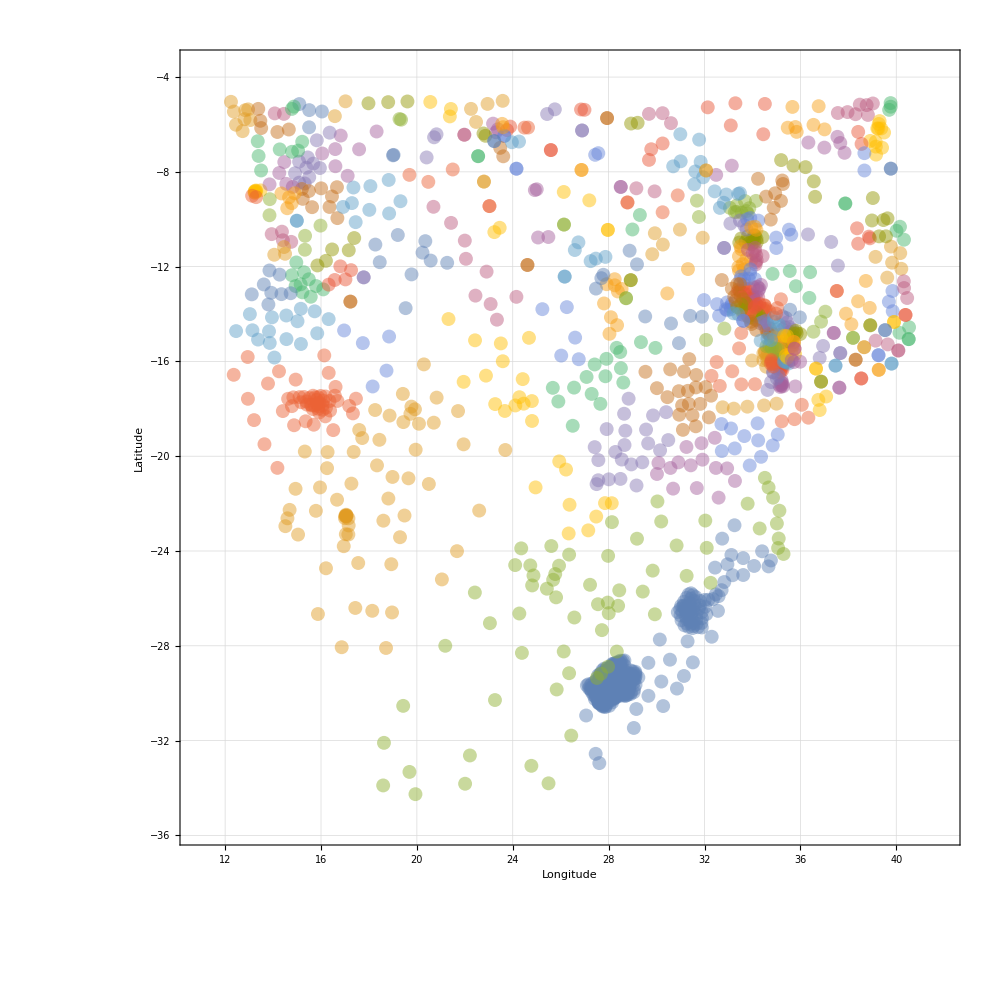

communitiesPlot.pdf

```mathematica
communitiesLongLats=Table[longlats[[#]]&/@i,{i,communities}];
ListPlot[communitiesLongLats
,AspectRatio->1
,Background->White
,Frame->True
,FrameLabel->(Style[#,50]&/@{"Longitude","Latitude"})
,FrameStyle->Thick
,FrameTicks->Automatic
,GridLines->Automatic
,GridLinesStyle->Opacity[.05]
,ImageSize->1000
,PlotStyle->Directive[PointSize[.01],Opacity[.475]]
,PlotRange->{{Min[longlats[[All,1]]]-1.5,Max[longlats[[All,1]]]+1.5},{Min[longlats[[All,2]]]-1.5,Max[longlats[[All,2]]]+1.5}}
]
Export["communitiesPlot.pdf",%]
```